```mathematica
(*P50 HW9*)
(*Each question is worth 1 pt. You can type your answer directly below the questions. Please upload your solution in .nb or .pdf*)

(*Q1: Simplify DiracDelta[10 x, 5 y, 2 z]. Your answer should be in the form of product of DiracDelta[x], DiracDelta[y] and DiracDelta[z]. *}
```

```mathematica
DiracDelta[10x,5y,2z]//FunctionExpand
```

1/100 DiracDelta[x] DiracDelta[y] DiracDelta[z]

```mathematica
(*Q2: Simplify DiracDelta[10 (x^2-1), 5 (y^2-2 y -3), 2 z]. Your answer should be in the form of linear combinations of products of DiracDelta[x+a], DiracDelta[y+b] and DiracDelta[z+c]. *}
```

```mathematica
DiracDelta[10(x^2-1),5(y^2-2y-3),2z]//FunctionExpand
```

1/800 DiracDelta[-1+x] DiracDelta[-3+y] DiracDelta[z]+1/800 DiracDelta[1+x] DiracDelta[-3+y] DiracDelta[z]+1/800 DiracDelta[-1+x] DiracDelta[1+y] DiracDelta[z]+1/800 DiracDelta[1+x] DiracDelta[1+y] DiracDelta[z]

```mathematica
(*Q3: Find the FourierTransform of DiracDelta[t^2-1]. *}
```

```mathematica
f3=DiracDelta[t^2-1]//FunctionExpand
FourierTransform[f3,t,ω]
```

1/2 DiracDelta[-1+t]+1/2 DiracDelta[1+t]

(ⅇ^(-ⅈ ω) (1+ⅇ^(2 ⅈ ω)))/(2 √(2 π))

```mathematica
(*Q4: Let's consider a dampled harmonic oscillator y[t] with an external force f[t]:
y''[t] + 3 y'[t] + 25/4 y[t]== f[t], where f[t] = Piecewise[{{0,t<5},{1,5<t<=15},{0,t>15}}]. The initial consitions are y[0] = 0 and y'[0] = 0.
Please use Green's function method to solve this ODE. *}
```

```mathematica
G1=GreenFunction[{y''[t]+3y'[t]+(25y[t])/4,y[0]==0,y'[0]==0},y[t],{t,0,∞},t1]//FullSimplify
solG1=Integrate[G1*Piecewise[{{0,t1<5},{1,5<t1<=15},{0,t1>15}}],{t1,0,t},Assumptions->t∈Reals]
```

1/2 ⅇ^(-3/2 (t-t1)) HeavisideTheta[t-t1] Sin[2 (t-t1)]

Piecewise[{{1/25 ⅇ^(-3 t/2) (4 ⅇ^(3 t/2)-4 ⅇ^(15/2) Cos[2 (-5+t)]+3 ⅇ^(15/2) Sin[10-2 t]), 5<t≤15}, {1/25 ⅇ^(15/2-(3 t)/2) (4 ⅇ^15 Cos[30-2 t]-4 Cos[2 (-5+t)]+3 Sin[10-2 t]-3 ⅇ^15 Sin[30-2 t]), t>15}, {0, True}}]

```mathematica
(* Q5: Use DSolve the solve the previous ODE. Plot both results and verify that they are the same.  *)
```

{{y[t]→Piecewise[{{1/25 ⅇ^(-3 t/2) (4 ⅇ^(3 t/2)-4 ⅇ^(15/2) Cos[2 (-5+t)]+3 ⅇ^(15/2) Sin[10-2 t]), 5<t≤15}, {1/25 ⅇ^(-3/2 (-5+t)) (4 ⅇ^15 Cos[30-2 t]-4 Cos[2 (-5+t)]+3 Sin[10-2 t]-3 ⅇ^15 Sin[30-2 t]), t>15}, {0, True}}]}}

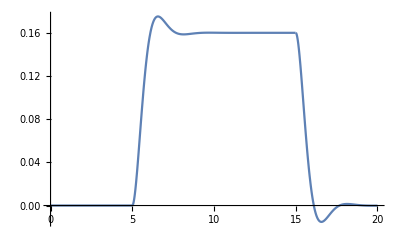

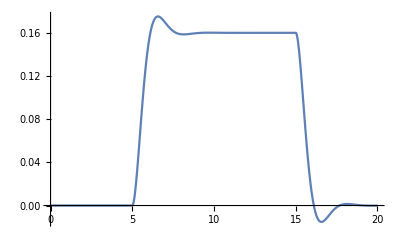

```mathematica
dsol=DSolve[{y''[t]+3y'[t]+(25y[t])/4==Piecewise[{{0,t<5},{1,5<t<=15},{0,t>15}}],y[0]==0,y'[0]==0},y[t],t]//Simplify
Plot[solG1,{t,0,20}]
Plot[y[t]/.dsol,{t,0,20}]
```

```mathematica
(*Q6: Let's consider a dampled harmonic oscillator y[t] with an external force f[t]:
y''[t] + 3 y'[t] + 25/4 y[t]== f[t], where f[t] = Piecewise[{{0,t<5},{Cos[t],5<t<=15},{0,t>15}}]. The initial consitions are y[0] = 0 and y'[0] = 0.
Please use Green's function method to solve this ODE. Then plot the solutition in the same plot with the solution in problem 4.*}
```

1/2 ⅇ^(-3/2 (t-t2)) HeavisideTheta[t-t2] Sin[2 (t-t2)]

Piecewise[{{1/390 ⅇ^(15/2-(3 t)/2) (-30 Cos[5-2 t]-26 Cos[15-2 t]+30 ⅇ^15 Cos[15-2 t]+26 ⅇ^15 Cos[45-2 t]+45 Sin[5-2 t]+13 Sin[15-2 t]-45 ⅇ^15 Sin[15-2 t]-13 ⅇ^15 Sin[45-2 t]), t>15}, {1/390 ⅇ^(-3 t/2) (-30 ⅇ^(15/2) Cos[5-2 t]-26 ⅇ^(15/2) Cos[15-2 t]+56 ⅇ^(3 t/2) Cos[t]+45 ⅇ^(15/2) Sin[5-2 t]+13 ⅇ^(15/2) Sin[15-2 t]+32 ⅇ^(3 t/2) Sin[t]), 5<t≤15}, {0, True}}]

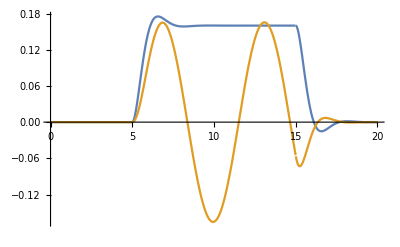

```mathematica
G2=GreenFunction[{y''[t]+3y'[t]+(25y[t])/4,y[0]==0,y'[0]==0},y[t],{t,0,∞},t2]//FullSimplify
solG2=Integrate[G2*Piecewise[{{0,t2<5},{Cos[t2],5<t2<=15},{0,t2>15}}],{t2,0,t},Assumptions->t∈Reals]
Plot[{solG1,solG2},{t,0,20}]
```